# ToneAr/LocalDeploy

Locally deploy async HTTP server able to emulate the Wolfram Cloud

## Paclet Manifest

"Documentation"

"English"

"Guides"

"ReferencePages"

"Symbols"

"LocalDeploymentObject.nb"DocumentationEnglishReferencePagesSymbolsLocalDeploymentObject.nb

"LocalDeployments.nb"DocumentationEnglishReferencePagesSymbolsLocalDeployments.nb

"LocalDeploy.nb"DocumentationEnglishReferencePagesSymbolsLocalDeploy.nb

"Tutorials"

"Kernel"

"LocalDeploy.wl"KernelLocalDeploy.wl

"Private.wl"KernelPrivate.wl

"Public.wl"KernelPublic.wl

"Source"

"Common.wl"KernelSourceCommon.wl

"Deployment.wl"KernelSourceDeployment.wl

"HTTP.wl"KernelSourceHTTP.wl

"Objects.wl"KernelSourceObjects.wl

"LocalDeploy-Definition.nb"LocalDeploy-Definition.nb

"PacletInfo.wl"PacletInfo.wl

"README.md"README.md

"Resources"

"Icons"

"icon.svg"ResourcesIconsicon.svg

"Tests"

"LocalDeploy.wlt"ResourcesTestsLocalDeploy.wlt

## Web Content

### Headline Image

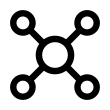

### Basic Description

Locally deploy HTTP servers able to emulate the Wolfram Cloud using GenerateHTTPResponse.

### Details

LocalDeploy creates a SocketListener on the specified port which has a HandlerFunction to compute and return a result from the api as an HTTP/1.1 response.

Fully async request hadnling.

LocalDeploy will return a LocalDeploymentObject representing the deployment containing all metainformation.

Responses are generated using GenerateHTTPResponse.

### Primary Context

ToneAr`LocalDeploy`

### Main Guide Page

## Examples

### Initialization for Examples

```mathematica
PacletDirectoryLoad[NotebookDirectory[]];
Get["ToneAr`LocalDeploy`"]
```

### Basic Examples

Deploy an APIFunction on an available port:

```mathematica
localDeployment = LocalDeploy[
APIFunction[{
"x"->"Number"
},
#x^2&
],
8888
]
```

LocalDeploymentObject[…]

The deployed API can be called using URLExecute:

```mathematica
URLExecute[localDeployment,{
"x" -> 10
}]
```

100

This is the same as doing:

```mathematica
URLExecute[localDeployment["URL"],{
"x" -> 10
}]
```

100

A port to deploy on can be specified using a second argument:

```mathematica
api = APIFunction[{
"x"->"Number",
"y"->"String"
},
{
#x^2,
StringReverse[#y]
}&,
"WXF"
];
localDeployment8000 = LocalDeploy[
api,
8000,
"HostAddress" -> "0.0.0.0"
]
```

LocalDeploymentObject[…]

Make a request to the API, importing the response data as a WXF:

```mathematica
URLExecute[localDeployment8000,{
"x" -> 10,
"y"->"abc"
}]
```

{100,cba}

Both Close and DeleteObject will close the sockets associated with the deployments:

```mathematica
Close[localDeployment8000]
```

0.0.0.0:8000

```mathematica
DeleteObject[localDeployment]
```

127.0.0.1:8888

## Source & Additional Information

### Creator

Antonis Aristeidou

### Source Control Repository

https://github.com/ToneAr/LocalDeploy

### License

MIT License [»](https://resources.wolframcloud.com/PacletRepository/licenses/MIT)
 Apache License 2.0 [»](https://resources.wolframcloud.com/PacletRepository/licenses/Apache-2.0)
 Creative Commons Zero v1.0 Universal [»](https://resources.wolframcloud.com/PacletRepository/licenses/CC0-1.0)
 NoneA license is not required for personal deployments

### Keywords

Local

Socket

TCP

Server

HTTP

Deploy

API

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Machine Learning
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction

### Related Resource Objects

### Original Source References and Attributions

### Links

### Compatibility

#### Wolfram Language Version

12.2+

#### Operating System

Windows |  Mac |  Linux

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

### Disclosures

Local filesDisclosuresLocalFilesChoose this option if your paclet directly does any of the following during loading or normal usage:
◼ Creates, deletes or modifies local files
◼ Imports data from local files
File operations related to normal paclet installation and loading are excepted.Click for more information

Wolfram accountDisclosuresWolframAccountChoose this option if your paclet directly does any of the following:
◼ Requires, uses, or records any information related to user’s Wolfram ID
◼ Interacts with the user’s Cloud account or Wolfram account
◼ Creates, deletes or modifies the user’s cloud objects
◼ Creates or executes cloud deployed scheduled tasks
◼ Uses cloud credits, service credits or Wolfram credits
◼ Makes WolframAlpha callsClick for more information

External servicesDisclosuresExternalServicesChoose this option if your paclet directly does any of the following:
◼ Makes requests to external services (http, ftp, ssh, etc)
◼ Creates or uses service connection
◼ Send emailsClick for more information

Wolfram Language system configurationDisclosuresWLSystemConfigurationChoose this option if your paclet directly does any of the following:
◼ Creates persistent local scheduled tasks
◼ Modifies WL system or environment settings
◼ Modifies $Path, Directory, or similar
◼ Installs additional paclets or dependencies
◼ Creates or imports non-public ResourceObject content
◼ Makes FrontEnd modifications
◼ Internal handlersClick for more information

Wolfram Language built-in symbolsDisclosuresWLSystemSymbolsChoose this option if your paclet directly modifies definitions of built-in symbols such as those in System` or other internal contexts.Click for more information

Paclet dependenciesDisclosuresPacletDependenciesChoose this option if your paclet directly installs or updates any additional paclets. Paclets that are included with the Wolfram system do not require a disclosure.Click for more information

OS configurationDisclosuresOSConfigurationChoose this option if your paclet directly does any of the following:
◼ Modifies OS settings
◼ Makes any use of SystemCredentialClick for more information

Local system interactionsDisclosuresLocalSystemInteractionsChoose this option if your paclet directly does any of the following:
◼ Executes Shell or RUN commands
◼ Uses external evaluators via ExternalEvaluate
◼ Interacts with external libraries
◼ Reads or writes to streams or sockets
◼ Launches parallel kernels, subkernels or GPUsClick for more information

OtherDisclosuresOtherAdd additional text as needed in a new cell below to document any additional disclosures that are not listed above.Click for more information

## Author Notes

2.0.0 - v2 Release
	Async functionality
	OverwriteExisting option

2.0.1 - Handle StringExpressions in endpoint generation for URLDispatcher